```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Processes/qq-mm/input/equivalence_classes.m

## Backup

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
```

```mathematica
sm=Table[<<(NotebookDirectory[]<>"interferences/Contribution_"<>ToString[i]<>"_1.m"),{i,376}];
```

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
Length[si]
```

2208

```mathematica
if=Cases[si,userIntegral[name_,mass_,__]:>name,Infinity]//DeleteDuplicates;
Print[AlphabeticSort[Map[ToString[#]&,if]]]
Length[if]
```

{A1,A2,A3,A4,A5,A6,B1,B2,B3,B4,B5,B6,B7,C1,C2,C3,C4,C5,C6,C7,C8,D1}

22

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");diagramCoefficients=<<(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
```

```mathematica
xiMasters={};
xiMastersW={};
xiMastersZ={};
Do[
If[!FreeQ[masters[[i]],GaugeXi[_]],
xiMasters=AppendTo[xiMasters,i];
If[!FreeQ[Cases[masters[[i]],mz*Sqrt[GaugeXi[_]],Infinity],mz],
xiMastersZ=AppendTo[xiMastersZ,i]
];
If[!FreeQ[Cases[masters[[i]],mw*Sqrt[GaugeXi[_]],Infinity],mw],
xiMastersw=AppendTo[xiMastersW,i]
]
]
,{i,Length[masters]}]
xiMasters
xiMastersZ
xiMastersW
Print["Tot: ",Length[xiMasters], " Z: ",Length[xiMastersZ], " W: ", Length[xiMastersW]]
```

{4,5,9,10,11,12,13,14,18,19,20,27,28,29,30,31,32,33,34,35,36,37,38,41,42,43,45,46,48,56,57,59,60,61,62,63,64,65,78,79,80,81,82,83,88,89,90,91,93,94,103,104,105,106,107,108,109,111,112,113,115,116,121,122,123,124,125,126,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,163,164,165,173,174,175,176,177,178,179,187,188,189,190,191,192,193,200,201,202,215,216,217,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,239,240,245,246,247,248,249,250,251,252,257,258,259,260,262,263,265,267,292,293,294,296,297}

{4,5,9,10,11,18,19,20,27,28,29,30,31,37,38,41,42,57,59,60,61,62,63,64,65,78,79,80,88,89,90,103,104,105,109,111,112,121,122,123,124,125,126,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,163,164,165,173,174,175,176,177,178,179,187,188,189,190,191,192,193,200,201,202,215,216,217,221,222,223,224,225,226,227,228,229,230,231,239,240,245,246,247,248,257,258,259,260,292,293,294,296,297}

{12,13,14,32,33,34,35,36,43,45,46,48,56,81,82,83,91,93,94,106,107,108,113,115,116,232,233,234,235,236,249,250,251,252,262,263,265,267}

Tot: 149 Z: 111 W: 38

```mathematica
totalCoefficients=<<(NotebookDirectory[]<>"final_results/totalCoefficientsS.m");
diagramCoefficientsRep=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
totalCoefficientsRep=<<(NotebookDirectory[]<>"final_results/totalCoefficientsRep.m");
totalCoefficientsRepCharge=<<(NotebookDirectory[]<>"final_results/totalCoefficientsRepCharge.m");
```

## Computations

## Total Coefficients

### Save

```mathematica
diagramCoefficientsRep={};
Do[Print[i];
diagramCoefficientsRep=AppendTo[diagramCoefficientsRep,Simplify[diagramCoefficients[[i]]/.parameterReplace/.{cw->Sqrt[1-sw^2],mw->mz*Sqrt[1-sw^2]}]]
,{i,Length[diagramCoefficients]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

```mathematica
diagramCoefficientsRep>>(NotebookDirectory[]<>"final_results/totalCoefficientsRep.m");
```

```mathematica
Variables[totalCoefficientsRep]
```

{d,EL,I3d,I3l,I3N,I3u,mb,mc,md,me,mh,ml,mm,ms,mt,mu,mz,Qd,Ql,Qu,s,sw,t,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
diagramCoefficientsRepCharge={};
Do[Print[i];
diagramCoefficientsRepCharge=AppendTo[diagramCoefficientsRepCharge,Simplify[diagramCoefficientsRep[[i]]/.chargeReplace]]
,{i,Length[diagramCoefficients]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

## Manipulation

```mathematica
xiMasters
Length[xiMasters]
```

{4,5,9,10,11,12,13,14,18,19,20,27,28,29,30,31,32,33,34,35,36,37,38,41,42,43,45,46,48,56,57,59,60,61,62,63,64,65,78,79,80,81,82,83,88,89,90,91,93,94,103,104,105,106,107,108,109,111,112,113,115,116,121,122,123,124,125,126,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,163,164,165,173,174,175,176,177,178,179,187,188,189,190,191,192,193,200,201,202,215,216,217,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,239,240,245,246,247,248,249,250,251,252,257,258,259,260,262,263,265,267,292,293,294,296,297}

149

```mathematica
Off[General::stop]
```

```mathematica
Variables[totalCoefficientsRepCharge]
```

{d,EL,mb,mc,md,me,mh,ml,mm,ms,mt,mu,mz,s,sw,t,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
Do[
Print[i];
totalCoefficientsRepCharge[[i]]/.chargeReplace/.{mu->0,md->0}
,{i,Length[masters]}]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

Power::infy: Infinite expression \!\(\*FractionBox["1", SuperscriptBox["0", "2"]]\) encountered.

Infinity::indet: Indeterminate expression \!\(\*RowBox[{FractionBox[RowBox[{"24576", " ", SuperscriptBox["mm", "4"]}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "3"]}]], "-", FractionBox[RowBox[{"12288", " ", "d", " ", SuperscriptBox["mm", "4"]}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "3"]}]], "+", FractionBox["12288", RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "-", FractionBox[RowBox[{"12288", " ", "d"}], RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "+", FractionBox[RowBox[{"3072", " ", SuperscriptBox["d", "2"]}], RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "+", RowBox[{"\[LeftSkeleton]", "64", "\[RightSkeleton]"}], "+", FractionBox[RowBox[{"768", " ", SuperscriptBox["mm", "2"], " ", "t"}], RowBox[{SuperscriptBox["mz", "2"], " ", RowBox[{"(", RowBox[{SuperscriptBox["mh", "2"], "-", "s"}], ")"}], " ", "s", " ", SuperscriptBox["sw", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", FractionBox[RowBox[{"768", " ", "d", " ", SuperscriptBox["mm", "2"], " ", "t"}], RowBox[{SuperscriptBox["mz", "2"], " ", RowBox[{"(", RowBox[{SuperscriptBox["mh", "2"], "-", "s"}], ")"}], " ", "s", " ", SuperscriptBox["sw", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", FractionBox[RowBox[{"12288", " ", SuperscriptBox["mm", "2"], " ", SuperscriptBox["sw", "2"], " ", "t"}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", SuperscriptBox["mz", "2"]}], "+", "s"}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "-", FractionBox[RowBox[{"6144", " ", "d", " ", SuperscriptBox["mm", "2"], " ", SuperscriptBox["sw", "2"], " ", "t"}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", SuperscriptBox["mz", "2"]}], "+", "s"}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", RowBox[{"\[LeftSkeleton]", "107", "\[RightSkeleton]"}]}]\) encountered.

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

### Null Coefficient

```mathematica
count=0;
Do[
c=totalCoefficientsRep[[xiMasters[[i]]]];
If[c=!=0,
count++;
Print[xiMasters[[i]]]],
{i,Length[xiMasters]}]
count
```

4

5

9

10

11

12

13

14

18

19

20

29

30

31

32

33

34

35

36

38

41

42

43

45

46

48

59

60

61

63

64

65

78

79

80

81

82

83

88

89

90

91

93

94

103

104

105

106

107

108

109

111

112

113

115

116

121

122

123

124

125

126

138

139

141

142

143

144

145

146

148

149

150

151

152

153

154

155

156

163

164

165

173

174

175

176

177

178

179

187

188

189

190

191

192

193

201

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

239

240

245

246

247

248

249

250

251

252

257

258

259

260

262

263

265

267

292

293

133

### Null Coefficient (zero mass)

```mathematica
totalCoefficientsRepChargeNoMass=totalCoefficientsRepCharge/.{mu->0,md->0}
```

Power::infy: Infinite expression \!\(\*FractionBox["1", SuperscriptBox["0", "2"]]\) encountered.

Infinity::indet: Indeterminate expression \!\(\*RowBox[{FractionBox[RowBox[{"24576", " ", SuperscriptBox["mm", "4"]}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "3"]}]], "-", FractionBox[RowBox[{"12288", " ", "d", " ", SuperscriptBox["mm", "4"]}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "3"]}]], "+", FractionBox["12288", RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "-", FractionBox[RowBox[{"12288", " ", "d"}], RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "+", FractionBox[RowBox[{"3072", " ", SuperscriptBox["d", "2"]}], RowBox[{"s", "-", RowBox[{"d", " ", "s"}]}]], "+", RowBox[{"\[LeftSkeleton]", "64", "\[RightSkeleton]"}], "+", FractionBox[RowBox[{"768", " ", SuperscriptBox["mm", "2"], " ", "t"}], RowBox[{SuperscriptBox["mz", "2"], " ", RowBox[{"(", RowBox[{SuperscriptBox["mh", "2"], "-", "s"}], ")"}], " ", "s", " ", SuperscriptBox["sw", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", FractionBox[RowBox[{"768", " ", "d", " ", SuperscriptBox["mm", "2"], " ", "t"}], RowBox[{SuperscriptBox["mz", "2"], " ", RowBox[{"(", RowBox[{SuperscriptBox["mh", "2"], "-", "s"}], ")"}], " ", "s", " ", SuperscriptBox["sw", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", FractionBox[RowBox[{"12288", " ", SuperscriptBox["mm", "2"], " ", SuperscriptBox["sw", "2"], " ", "t"}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", SuperscriptBox["mz", "2"]}], "+", "s"}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "-", FractionBox[RowBox[{"6144", " ", "d", " ", SuperscriptBox["mm", "2"], " ", SuperscriptBox["sw", "2"], " ", "t"}], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "d"}], ")"}], " ", SuperscriptBox["s", "2"], " ", RowBox[{"(", RowBox[{RowBox[{"-", SuperscriptBox["mz", "2"]}], "+", "s"}], ")"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", SuperscriptBox["sw", "2"]}], ")"}]}]], "+", RowBox[{"\[LeftSkeleton]", "107", "\[RightSkeleton]"}]}]\) encountered.

{-(ⅈ EL^6 mm^2 ((8 (1))/(2-d)+(s (1+4+1))/(4 (-2+d) (mz^2-s) sw^2 (-1+sw^2))))/(1152 mz^2 π^4 s^2 (-4 mm^2+s)^2 sw^2 (1-sw^2)),(ⅈ EL^6 (1))/1,295,1/1,(ⅈ 2 (12 s^2-12 d s^2+18+1+2 mm^2 (-3 (6-5 d+d^2) s-4 (1) t)))/(4608 (-1+d) π^4 (mz^2-s)^2 s^2 sw^4 (-1+sw^2)^2)}
 |  |  |  |

```mathematica
count=0;
Do[
c=totalCoefficientsRepChargeNoMass[[xiMasters[[i]]]]//Simplify;
If[c=!=0,
count++;
Print[xiMasters[[i]]]],
{i,Length[xiMasters]}]
count
```

12

13

14

18

19

20

32

33

34

35

36

43

45

46

48

91

93

106

107

113

115

232

233

249

250

262

263

27

```mathematica
masters[[12]]
```

userIntegral[A3,{mw √GaugeXi[Q]},0,1,0,1]

```mathematica
totalCoefficientsRepChargeNoMass[[12]]//Simplify
```

(ⅈ EL^6 (s (64 (2-3 d+d^2) mm^10 (mz^2-s)-16 mm^8 (32 (-2+d) mz^4 sw^2 (-1+sw^2)+(-1+d) s ((11-10 d+2 d^2) s-8 (-2+d) t)+mz^2 (-s (13+9 d-12 d^2+2 d^3-48 sw^2+24 d sw^2)+8 (2-3 d+d^2) t))+(-2+d) mz^2 s^2 (s^3 (-12-4 d (-3+sw^2)+d^2 (-3+2 sw^2))-32 mz^2 sw^2 (-1+sw^2) t^2-4 s t (8 mz^2 sw^2 (-1+sw^2)+3 t-6 sw^2 t)-2 s^2 (4 (-2+d) mz^2 sw^2 (-1+sw^2)+(d^2 (3-2 sw^2)-24 (-1+sw^2)+5 d (-3+2 sw^2)) t))+8 mm^6 (32 (-2+d) mz^4 sw^2 (-1+sw^2) (s+4 t)+(-1+d) s ((33-27 d+5 d^2) s^2+4 (9-7 d+d^2) s t-8 (-2+d) t^2)+mz^2 (s^2 (d^3 (7-8 sw^2)+9 (-15+16 sw^2)-8 d (-18+19 sw^2)+d^2 (-52+56 sw^2))-4 s (15-8 d^2+d^3-48 sw^2+4 d (1+6 sw^2)) t+8 (2-3 d+d^2) t^2))-4 mm^4 ((-1+d) s^2 ((30-23 d+4 d^2) s^2+2 (14-15 d+3 d^2) s t-4 t^2)+8 (-2+d) mz^4 sw^2 (-1+sw^2) ((-7+4 d) s^2+32 s t+16 t^2)+mz^2 s (-(-2+d) s^2 (d (89-56 sw^2)+54 (-2+sw^2)+4 d^2 (-5+4 sw^2))-2 s (226-288 sw^2+d^2 (66-56 sw^2)+d^3 (-9+8 sw^2)+d (-211+224 sw^2)) t+4 (-25+48 sw^2+d (13-24 sw^2)) t^2))+2 mm^2 s ((-1+d) s^2 ((8-6 d+d^2) s^2+2 (4-5 d+d^2) s t-4 t^2)+32 (-2+d) mz^4 sw^2 (-1+sw^2) ((-2+d) s^2+5 s t+4 t^2)-2 mz^2 s ((-2+d) s^2 (-31+6 sw^2+d (29-13 sw^2)+d^2 (-7+5 sw^2))+s (200-216 sw^2+d^2 (78-56 sw^2)+d^3 (-11+8 sw^2)+d (-213+188 sw^2)) t+2 (25-48 sw^2+d (-13+24 sw^2)) t^2)))-4 mz^2 (-1+sw^2) (-16 (-2+d) mm^8 (-(-1+d) s^2-32 mz^4 sw^2 (-1+sw^2)+mz^2 s (-13+d+24 sw^2))-(-2+d) mz^2 s^2 (s^3 (-12-4 d (-3+sw^2)+d^2 (-3+2 sw^2))-32 mz^2 sw^2 (-1+sw^2) t^2-4 s t (8 mz^2 sw^2 (-1+sw^2)+3 t-6 sw^2 t)-2 s^2 (4 (-2+d) mz^2 sw^2 (-1+sw^2)+(d^2 (3-2 sw^2)-24 (-1+sw^2)+5 d (-3+2 sw^2)) t))-4 mm^6 (64 (-2+d) mz^4 sw^2 (-1+sw^2) (s+4 t)+(-1+d) s^2 ((11-10 d+2 d^2) s+8 (-2+d) t)+mz^2 s (s (-325+288 sw^2+d (387-304 sw^2)+d^3 (22-16 sw^2)+4 d^2 (-39+28 sw^2))-8 (26+d^2-48 sw^2+3 d (-5+8 sw^2)) t))+2 mm^4 (16 (-2+d) mz^4 sw^2 (-1+sw^2) ((-7+4 d) s^2+32 s t+16 t^2)+(-1+d) s^2 ((22-17 d+3 d^2) s^2+4 (1-3 d+d^2) s t+8 (-2+d) t^2)+mz^2 s (-(-2+d) s^2 (-235+108 sw^2+d (202-112 sw^2)+d^2 (-45+32 sw^2))-4 s (239-288 sw^2+d^2 (80-56 sw^2)+d^3 (-11+8 sw^2)+4 d (-59+56 sw^2)) t-8 (26+d^2-48 sw^2+3 d (-5+8 sw^2)) t^2))+mm^2 s (-(-1+d) s^2 ((8-6 d+d^2) s^2+2 (4-5 d+d^2) s t-4 t^2)-64 (-2+d) mz^4 sw^2 (-1+sw^2) ((-2+d) s^2+5 s t+4 t^2)+mz^2 s ((-2+d) s^2 (d (121-52 sw^2)+8 (-16+3 sw^2)+d^2 (-29+20 sw^2))+2 s (404-432 sw^2+d^3 (-23+16 sw^2)-2 d^2 (-81+56 sw^2)+d (-435+376 sw^2)) t+4 (49-96 sw^2+d (-25+48 sw^2)) t^2))) GaugeXi[Q]))/(1536 (-2+d) (-1+d) mz^4 π^4 (mz^2-s) s^2 (-4 mm^2+s)^2 sw^4 (-1+sw^2)^2)

```mathematica
l=diagramContributionList[diagramCoefficientsRepCharge,12]
```

{7,15,19,23,29,32,39,41,42,43,201,204,205,207,208,217,357,358,359,361,362,363,364,365,366,367,368,369,371,372,373,374,375,376}

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

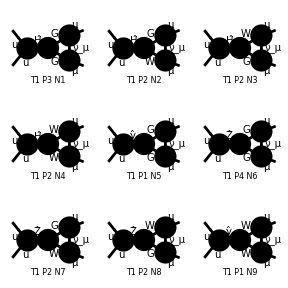

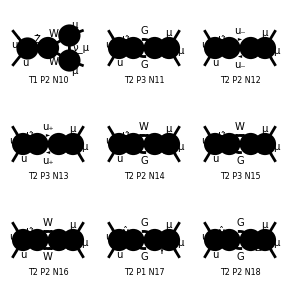

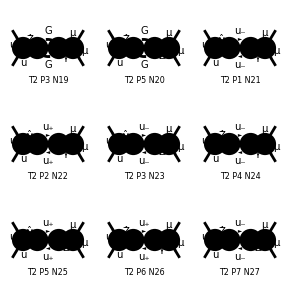

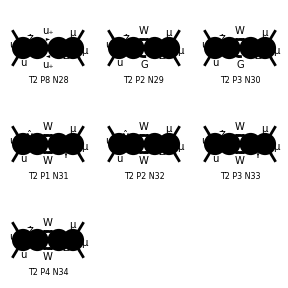

FeynArtsGraphics[{u,u}→{\mu,\mu}][([T1 P3 N1] | [T1 P2 N2] | [T1 P2 N3]
[T1 P2 N4] | [T1 P1 N5] | [T1 P4 N6]
[T1 P2 N7] | [T1 P2 N8] | [T1 P1 N9]),([T1 P2 N10] | [T2 P3 N11] | [T2 P2 N12]
[T2 P3 N13] | [T2 P2 N14] | [T2 P3 N15]
[T2 P2 N16] | [T2 P1 N17] | [T2 P2 N18]),([T2 P3 N19] | [T2 P5 N20] | [T2 P1 N21]
[T2 P2 N22] | [T2 P3 N23] | [T2 P4 N24]
[T2 P5 N25] | [T2 P6 N26] | [T2 P7 N27]),([T2 P8 N28] | [T2 P2 N29] | [T2 P3 N30]
[T2 P1 N31] | [T2 P2 N32] | [T2 P3 N33]
[T2 P4 N34] | Null | Null)]

```mathematica
Paint[DiagramExtract[fields1L,l]]
```

## Tools

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
```

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

### Scalar integrals maipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

```mathematica
diagramContributionList[coefflist_List,n_Integer]:=Module[{result,contr},
If[MatrixQ[coefflist],
result={};
contr=contributions[coefflist];
Do[
If[contr[[i,n]]===1,
result=AppendTo[result,i]
]
,{i,Length[contr]}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```